```mathematica
Clear[ω]
```

```mathematica
ω[k_]:=√(g k Tanh[Subscript[H, 0] k])
```

```mathematica
Cp[k_]:=Simplify[ω[k]/k,{k∈Reals,k>0}]
```

```mathematica
Cg[k_]=FullSimplify[D[ω[k],k],{k∈Reals,k>0}]
```

(g (k Sech[k H_0]^2 H_0+Tanh[k H_0]))/(2 √(g k Tanh[k H_0]))

```mathematica
pCg:=LogLinearPlot[Cg[k]/.{Subscript[H, 0]->1,g->1},{k,0.0001,100}]
```

```mathematica
pCp:=LogLinearPlot[Cp[k]/.{Subscript[H, 0]->1,g->1},{k,0.0001,100}]
```

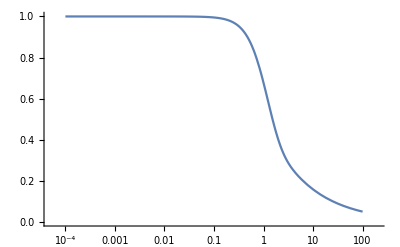

```mathematica
Show[pCg]
```

```mathematica
Ω[k_,a_]:=k √((1+(a-1)/3(k H0)^2)/(1+a/3(k H0)^2))
```

```mathematica
Vp[k_]:=Simplify[Ω[k,a]/k,{{k,a}∈Reals,{k,a}>0}]/.a->1
```

```mathematica
Vg[k_]:=Simplify[D[Ω[k,a],k],{{k,a}∈Reals,{k,a}>0}]/.a->1
```

```mathematica
Vp[k]
```

√3 √(1/(3+H0^2 k^2))

```mathematica
Vg[k]
```

3 √3 (1/(3+H0^2 k^2))^(3/2)

```mathematica
pVp:=LogLinearPlot[Vp[k]/.{H0->1},{k,0.0001,100}]
```

```mathematica
pVg:=LogLinearPlot[Vg[k]/.{H0->1},{k,0.0001,100}]
```

```mathematica
Show[pVg]
```

General::ivar: 0.000100028 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-